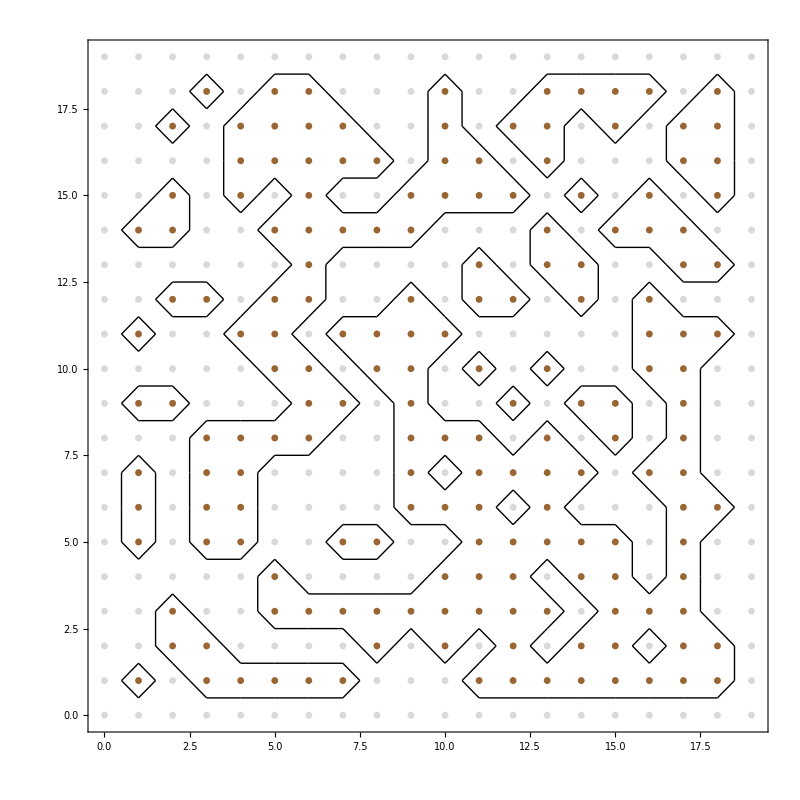

```mathematica
data=Import[NotebookDirectory[]<>"out/x64-Debug/output-boundary.txt","Table"];
data=Partition[#,2]&/@data;

rawdata=Import[NotebookDirectory[]<>"out/x64-Debug/output-raw.txt","Table"];
disks=MapIndexed[{If[#1==1,Brown,LightGray],Disk[#2-{1,1},0.1]}&,Transpose@rawdata,{2}];

Graphics[{disks,Line[data]},ImageSize->800,Frame->True]
```